```mathematica
Quit[]
```

NFW OF LMC

```mathematica
SolarMass=1.988 10^(30);(*Kg*)
eVtoKg=1.782662×10^(-36) ;(*Kg*)
pc=3.0857 10^(16) ;(*in m*)
rs=9.8;(*kpc*)
ρs=5.1 10^6  SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3) (*GeV cm-3*)
NFW[r_]:=ρs rs/r (1+r/rs)^(-2);
NFW[50]
```

0.193578

0.00101897

```mathematica
pc=3.0857 10^(16) ;(*in m*)
Kpc=10^3 pc;(*pc*)
d=50.;(*kpc*)
Profile[r_]:=NFW[r]
RGCθ[s_,θ_]:=Module[{x,y,z},z=s Sin[θ];y=0;x=d-s Cos[θ];Sqrt[x^2+y^2+z^2]]
step=1.;
LosDθ[θ_]:=(Kpc 10^2)(NIntegrate[Profile[RGCθ[s,θ]],{s,0.,d-step}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d-step,d+step},Method->{Automatic,"SymbolicProcessing" -> 0}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d+step,1.5d}])
```

```mathematica
LosDθ[0.1]
```

7.62461×10^21

InterpolatingFunction[…]

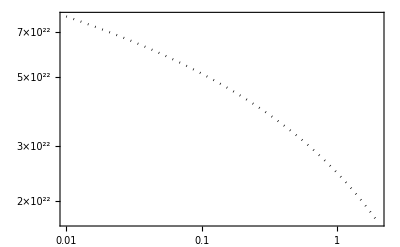

```mathematica
Npoints=100;
θmin=0.01;
θmax=2.;
Do[aθ[i]=10^(Log10[θmin]+Log10[θmax/θmin]*i/Npoints) Pi/180;(*rad*)
aIntelosθ[i]=LosDθ[aθ[i]],{i,0,Npoints}]
dDdΩθLogLog=Interpolation[Table[{Log10@aθ[i],Log10@aIntelosθ[i]},{i,0,Npoints}],InterpolationOrder->1]
dDdΩ[x_]:=10^(dDdΩθLogLog[Log10[x]])
dDdΩ[x_]:=10.^(dDdΩθLogLog[Log10[x]])
LogLogPlot[{dDdΩ[α Pi/180]},{α,θmin ,θmax},Frame->True,PlotStyle->{Darker[Green],{Black,Dotted}}(*,FrameLabel->{StyleFrameLabel["θ [rad]"],StyleFrameLabel["dD/dΩ(α) [GeV cm^-2sr^-1]"]},
FrameStyle-> StyleFrameTicks*)
]
```

```mathematica
αint=3.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 1.5825×10^20 for θ [deg] 3.

D GeV cm-2 1.5825×10^20 for θ [deg] 3.

D GeV cm-2 5.55238×10^19 for θ [deg] 1.5

NFW OF MW

```mathematica
(*NFW from Cirelli-Strumia-Zupan*)
rs=14.46;(*kpc*)
ρs=0.566;(*GeV cm-3*)
Rsun=8.33;(*kpc*)
NFW[r_]:=ρs rs/r (1+r/rs)^(-2)
Profile[r_]:=NFW[r]
RGC[s_,l_,b_]:=Module[{x,y,z},z=s Sin[b];y=s Cos[b]Sin[l];x=Rsun-s Cos[b]Cos[l];Sqrt[x^2+y^2+z^2]]
RGCθ[s_,θ_]:=Module[{x,y,z},z=s Sin[θ];y=0;x=Rsun-s Cos[θ];Sqrt[x^2+y^2+z^2]]
pc=3.0857 10^(16) ;(*in m*)
Kpc=10^3 pc;(*pc*)
step=0.5;
(*Output in GeV cm-2*)
LosD[l_,b_]:=(Kpc 10^2)(NIntegrate[Profile[RGC[s,l,b]],{s,0.,Rsun-step}]+NIntegrate[Profile[RGC[s,l,b]],{s,Rsun-step,Rsun+step},Method->{Automatic,"SymbolicProcessing" -> 0}]+NIntegrate[Profile[RGC[s,l,b]],{s,Rsun,1.5Rsun}])
LosDθ[θ_]:=(Kpc 10^2)(NIntegrate[Profile[RGCθ[s,θ]],{s,0.,Rsun-0.1}]+NIntegrate[Profile[RGCθ[s,θ]],{s,Rsun-0.1, Rsun+0.1}]+NIntegrate[Profile[RGCθ[s,θ]],{s,Rsun+0.1,10 Rsun}])
```

```mathematica
(*(*From SPHEREX notebook as a check*)
lNGC=96.38 Pi/180;
bNGC=29.81 Pi/180;
lmin=lNGC-5.4Pi/180;
lmax=lNGC+5.4Pi/180;
bmin=bNGC-5.4Pi/180;
bmax=bNGC+5.4Pi/180;
ΔΩ=(lmax-lmin)(Sin[bmax]-Sin[bmin]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosDθ[Sqrt[lNGC^2+bNGC^2]]]
Dfact=LosDθ[Sqrt[lNGC^2+bNGC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact]
Dfact=LosD[lNGC,bNGC] ΔΩ;
Print["D GeV cm-2 ",Dfact]*)
```

ΔΩ in deg2 101.056

dD/dΩ GeV cm-2 sr-1 1.33482×10^22

D GeV cm-2 4.10904×10^20

D GeV cm-2 3.16824×10^20

```mathematica
lLMC=280.4652 Pi/180;
bLMC=-32.8884 Pi/180;
αint=1.5;
ΔΩ=2Pi (1-Cos[αint Pi/180.]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosDθ[Sqrt[lLMC^2+bLMC^2]]]
Dfact=LosDθ[Sqrt[lLMC^2+bLMC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
Dfact=LosD[lNGC,bNGC] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
```

ΔΩ in deg2 7.06818

dD/dΩ GeV cm-2 sr-1 1.76089×10^22

D GeV cm-2 3.79135×10^19 for α [deg] 1.5

D GeV cm-2 2.21597×10^19 for α [deg] 1.5

```mathematica
(*Coordinates LMC here https://simbad.u-strasbg.fr/simbad/sim-id?Ident=Large+Magellanic+Cloud*)
αint=3.0;
ΔΩ=2Pi (1-Cos[αint Pi/180.]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosDθ[Sqrt[lLMC^2+bLMC^2]]]
Dfact=LosDθ[Sqrt[lLMC^2+bLMC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
Dfact=LosD[lNGC,bNGC] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
```

ΔΩ in deg2 28.2679

dD/dΩ GeV cm-2 sr-1 1.76089×10^22

D GeV cm-2 1.51628×10^20 for α [deg] 3.

D GeV cm-2 8.86234×10^19 for α [deg] 3.

InterpolatingFunction[…]

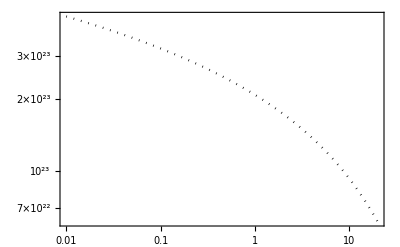

```mathematica
Npoints=300;
θmin=0.01;
θmax=20.;
Do[aθ[i]=10^(Log10[θmin]+Log10[θmax/θmin]*i/Npoints) Pi/180;(*rad*)
aIntelosθ[i]=LosDθ[aθ[i]],{i,0,Npoints}]
dDdΩθLogLog=Interpolation[Table[{Log10@aθ[i],Log10@aIntelosθ[i]},{i,0,Npoints}],InterpolationOrder->1]
dDdΩ[x_]:=10^(dDdΩθLogLog[Log10[x]])
dDdΩ[x_]:=10.^(dDdΩθLogLog[Log10[x]])
LogLogPlot[{dDdΩ[α Pi/180]},{α,θmin ,θmax},Frame->True,PlotStyle->{Darker[Green],{Black,Dotted}}(*,FrameLabel->{StyleFrameLabel["θ [rad]"],StyleFrameLabel["dD/dΩ(α) [GeV cm^-2sr^-1]"]},
FrameStyle-> StyleFrameTicks*)
]
```

```mathematica
Rsun
ρsun=Profile[Rsun]
```

8.33

0.395537

```mathematica
αint=3.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
(*ΔΩ=2Pi(1-Cos[αint/180.]);*)
(*dDdΩ[αint Pi/180 ]/(Rsun Kpc 100  ρsun) *)
```

D GeV cm-2 1.52379×10^21 for θ [deg] 3.

```mathematica
αint=10.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 1.11755×10^22 for θ [deg] 10.

```mathematica
αint=15.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 2.08901×10^22 for θ [deg] 15.

```mathematica
αint=20.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 3.19051×10^22 for θ [deg] 20.

Sterile Nu Decay rate
Eq.1 of https://arxiv.org/pdf/1911.09120

```mathematica
Quit[]
```

```mathematica
(7.2 10^(29))^(-1)
```

1.38889×10^-30

```mathematica
Solve[1/τ==(7.2 10^(29))^(-1) Sinsq2θ/(10^(-8)) mkeV^5,Sinsq2θ]
```

{{Sinsq2θ→(7.2×10^21)/(mkeV^5 τ)}}

```mathematica
(7.2 10^(21))^(-1)
```

1.38889×10^-22

```mathematica
(*Check consistency with eq. 4.13 of https://arxiv.org/pdf/1602.04816*)
```

```mathematica
Sinsq2θ=10^(-8);
θ=Sqrt[Sinsq2θ/4];
5.5 10^(-22) (θ)^2
(7.2 10^(29))^(-1)
```

1.375×10^-30

1.38889×10^-30